```mathematica
ClearAll["Global`*"]
```

## Initializer:

```mathematica
eq=Sqrt[(4*π)/137];
Bu=1/3;Qu=(2*eq)/3;Su=0;
Bd=1/3;Qd=-eq/3;Sd=0;
Bs=1/3;Qs=-eq/3;Ss=-1;
du=6;dd=6;ds=6;dg=16;
mu=0.001;md=0.001;ms=0.08;
```

## Distribution Functions:

```mathematica
fu[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+mu^2]-(Bu*mub+Qu*muq+Su*mus))/T]+1);
afu[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+mu^2]+Bu*mub+Qu*muq+Su*mus)/T]+1);
fd[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+md^2]-(Bd*mub+Qd*muq+Sd*mus))/T]+1);
afd[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+md^2]+Bd*mub+Qd*muq+Sd*mus)/T]+1);
fs[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+ms^2]-(Bs*mub+Qs*muq+Ss*mus))/T]+1);
afs[x_,T_,mub_,muq_,mus_]:=1/(Exp[(Sqrt[x^2+ms^2]+Bs*mub+Qs*muq+Ss*mus)/T]+1);
fut[x_,T_,mub_,muq_,mus_]:=1-fu[x,mub,muq,mus];
afut[x_,T_,mub_,muq_,mus_]:=1-afu[x,mub,muq,mus];
fdt[x_,T_,mub_,muq_,mus_]:=1-fd[x,mub,muq,mus];
afdt[x_,T_,mub_,muq_,mus_]:=1-afd[x,mub,muq,mus];
fst[x_,T_,mub_,muq_,mus_]:=1-fs[x,mub,muq,mus];
afst[x_,T_,mub_,muq_,mus_]:=1-afs[x,mub,muq,mus];
```

## Thermodynamic Integrals:

```mathematica
igpu[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=du/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+mu^2])^(n-2*q-1)*(fu[x,T,mub,muq,mus]+afu[x,T,mub,muq,mus]);
igmu[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=du/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+mu^2])^(n-2*q-1)*(fu[x,T,mub,muq,mus]-afu[x,T,mub,muq,mus]);
igpd[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=dd/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+md^2])^(n-2*q-1)*(fd[x,T,mub,muq,mus]+afd[x,T,mub,muq,mus]);
igmd[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=dd/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+md^2])^(n-2*q-1)*(fd[x,T,mub,muq,mus]-afd[x,T,mub,muq,mus]);
igps[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=ds/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+ms^2])^(n-2*q-1)*(fs[x,T,mub,muq,mus]+afs[x,T,mub,muq,mus]);
igms[x_?NumericQ,n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=ds/((2*q+1)!!)*(-1)^q/(2*π^2)*x^(2*q+2)*(Sqrt[x^2+ms^2])^(n-2*q-1)*(fs[x,T,mub,muq,mus]-afs[x,T,mub,muq,mus]);

ipu[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igpu[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];
imu[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igmu[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];
ipd[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igpd[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];
imd[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igmd[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];
ips[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igps[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];
ims[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=NIntegrate[igms[x,n,q,T,mub,muq,mus],{x,0,∞},AccuracyGoal->6];

jpu[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)ipu[n-1,q,T,mub,muq,mus]-ipu[n-1,q-1,T,mub,muq,mus]);
jmu[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)imu[n-1,q,T,mub,muq,mus]-imu[n-1,q-1,T,mub,muq,mus]);
jpd[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)ipd[n-1,q,T,mub,muq,mus]-ipd[n-1,q-1,T,mub,muq,mus]);
jmd[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)imd[n-1,q,T,mub,muq,mus]-imd[n-1,q-1,T,mub,muq,mus]);
jps[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)ips[n-1,q,T,mub,muq,mus]-ips[n-1,q-1,T,mub,muq,mus]);
jms[n_?NumericQ,q_?NumericQ,T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=T*((n-2*q)ims[n-1,q,T,mub,muq,mus]-ims[n-1,q-1,T,mub,muq,mus]);
```

## Necessary Variables :

```mathematica
nu[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=imu[1,0,T,mub,muq,mus];
nd[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=imd[1,0,T,mub,muq,mus];
ns[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=ims[1,0,T,mub,muq,mus];
nQ[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=Qu*nu[T,mub,muq,mus]+Qd*nd[T,mub,muq,mus]+Qs*ns[T,mub,muq,mus];
nB[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=Bu*nu[T,mub,muq,mus]+Bd*nd[T,mub,muq,mus]+Bs*ns[T,mub,muq,mus];
nS[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=Su*nu[T,mub,muq,mus]+Sd*nd[T,mub,muq,mus]+Ss*ns[T,mub,muq,mus];
et[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=ipu[2,0,T,mub,muq,mus]+ipd[2,0,T,mub,muq,mus]+ips[2,0,T,mub,muq,mus]+(8*π^2*T^4)/15;
pt[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-ipu[2,1,T,mub,muq,mus]-ipd[2,1,T,mub,muq,mus]-ips[2,1,T,mub,muq,mus]+(8*π^2*T^4)/45;
ht[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=et[T,mub,muq,mus]+pt[T,mub,muq,mus]
```

#### Conductivity Part (Diagonal) :

```mathematica
bbb[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Bu*Bu*jpu[1,1,T,mub,muq,mus]+Bd*Bd*jpd[1,1,T,mub,muq,mus]+Bs*Bs*jps[1,1,T,mub,muq,mus]+(T*nB[T,mub,muq,mus]*nB[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
bqq[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Qu*Qu*jpu[1,1,T,mub,muq,mus]+Qd*Qd*jpd[1,1,T,mub,muq,mus]+Qs*Qs*jps[1,1,T,mub,muq,mus]+(T*nQ[T,mub,muq,mus]*nQ[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
bss[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Su*Su*jpu[1,1,T,mub,muq,mus]+Sd*Sd*jpd[1,1,T,mub,muq,mus]+Ss*Ss*jps[1,1,T,mub,muq,mus]+(T*nS[T,mub,muq,mus]*nS[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
```

#### Conductivity Part (Off-Diagonal) :

```mathematica
bqb[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Qu*Bu*jpu[1,1,T,mub,muq,mus]+Qd*Bd*jpd[1,1,T,mub,muq,mus]+Qs*Bs*jps[1,1,T,mub,muq,mus]+(T*nQ[T,mub,muq,mus]*nB[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
bbs[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Bu*Su*jpu[1,1,T,mub,muq,mus]+Bd*Sd*jpd[1,1,T,mub,muq,mus]+Bs*Ss*jps[1,1,T,mub,muq,mus]+(T*nB[T,mub,muq,mus]*nS[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
bqs[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=-(Qu*Su*jpu[1,1,T,mub,muq,mus]+Qd*Sd*jpd[1,1,T,mub,muq,mus]+Qs*Ss*jps[1,1,T,mub,muq,mus]+(T*nQ[T,mub,muq,mus]*nS[T,mub,muq,mus])/(et[T,mub,muq,mus]+pt[T,mub,muq,mus]));
```

## Various Ratios :

```mathematica
Rbb[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bbb[T,mub,muq,mus]/T^3;
Rqq[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bqq[T,mub,muq,mus]/T^3;
Rss[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bss[T,mub,muq,mus]/T^3;
Rbq[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bqb[T,mub,muq,mus]/T^3;
Rbs[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bbs[T,mub,muq,mus]/T^3;
Rqs[T_?NumericQ,mub_?NumericQ,muq_?NumericQ,mus_?NumericQ]:=bqs[T,mub,muq,mus]/T^3;
```

## Code Test :

```mathematica
bqq[0.15,0.0,0.0,0.0]
```

0.0000676767

```mathematica
Rbb[0.2,0.0,0.0,0.0]
Rbb[0.2,0.3,0.0,0.0]
Rbb[0.2,0.6,0.0,0.0]
```

0.108875

0.105674

0.0983464

## Plots :

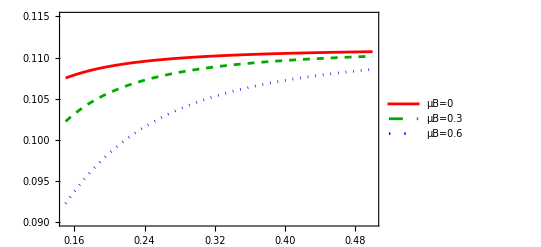

```mathematica
Plot[{Rbb[a,0.0,0.0,0.0],Rbb[a,0.3,0.0,0.0],Rbb[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.09,0.115}}]
```

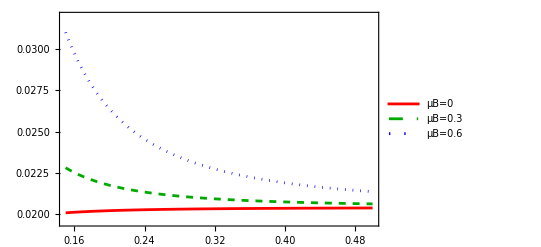

```mathematica
Plot[{Rqq[a,0.0,0.0,0.0],Rqq[a,0.3,0.0,0.0],Rqq[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.0195,0.032}}]
```

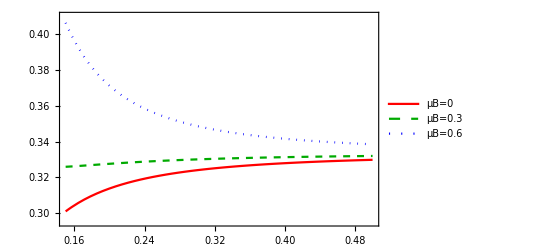

```mathematica
Plot[{Rss[a,0.0,0.0,0.0],Rss[a,0.3,0.0,0.0],Rss[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.295,0.41}}]
```

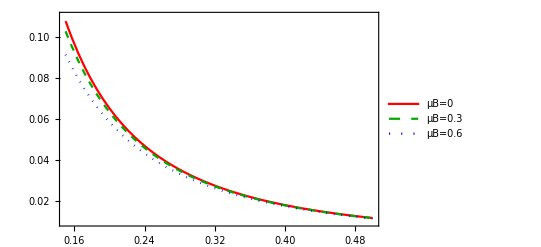

```mathematica
Plot[{100*Rbq[a,0.0,0.0,0.0],100*Rbq[a,0.3,0.0,0.0],100*Rbq[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.01,0.11}}]
```

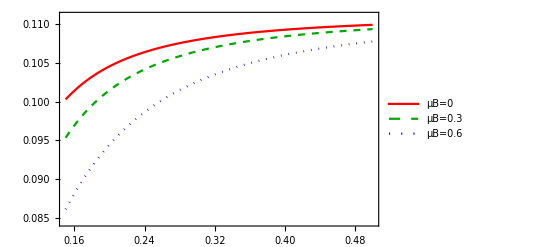

```mathematica
Plot[{-Rbs[a,0.0,0.0,0.0],-Rbs[a,0.3,0.0,0.0],-Rbs[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.0845,0.111}}]
```

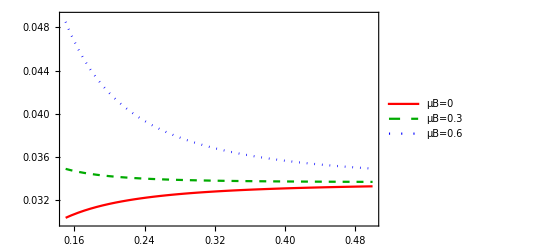

```mathematica
Plot[{Rqs[a,0.0,0.0,0.0],Rqs[a,0.3,0.0,0.0],Rqs[a,0.6,0.0,0.0]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μB=0","μB=0.3","μB=0.6"},PlotRange->{{0.15,0.5},{0.03,0.049}}]
```

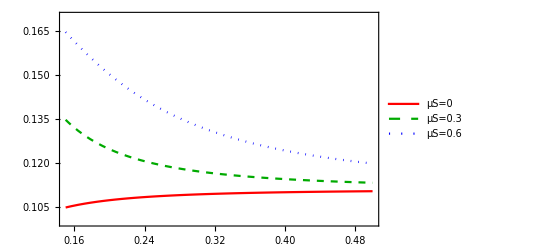

```mathematica
Plot[{Rbb[a,0.2,0.0,0.0],Rbb[a,0.2,0.0,0.3],Rbb[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{0.1,0.17}}]
```

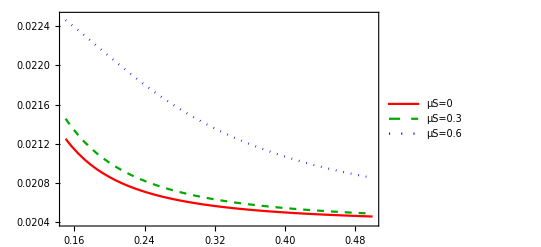

```mathematica
Plot[{Rqq[a,0.2,0.0,0.0],Rqq[a,0.2,0.0,0.3],Rqq[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{0.0204,0.0225}}]
```

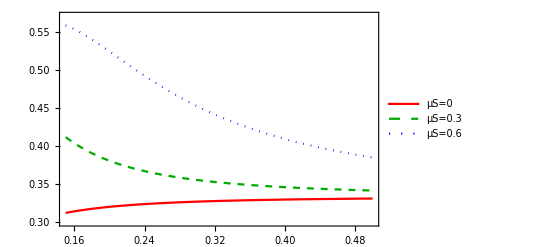

```mathematica
Plot[{Rss[a,0.2,0.0,0.0],Rss[a,0.2,0.0,0.3],Rss[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{0.3,0.57}}]
```

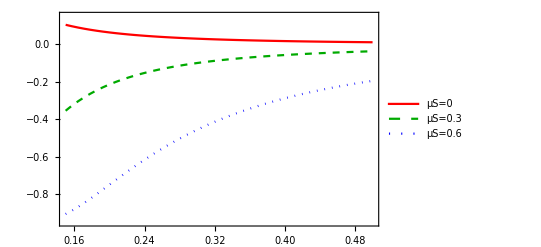

```mathematica
Plot[{100*Rbq[a,0.2,0.0,0.0],100*Rbq[a,0.2,0.0,0.3],100*Rbq[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{-0.95,0.15}}]
```

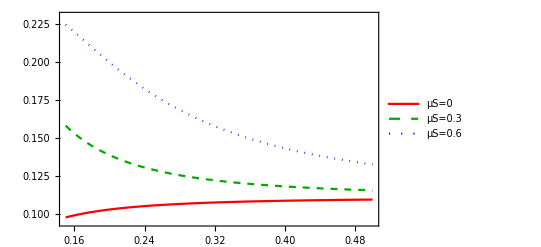

```mathematica
Plot[{-Rbs[a,0.2,0.0,0.0],-Rbs[a,0.2,0.0,0.3],-Rbs[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{0.095,0.23}}]
```

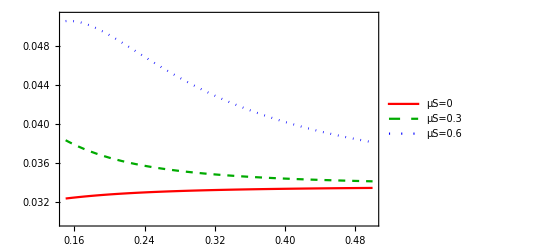

```mathematica
Plot[{Rqs[a,0.2,0.0,0.0],Rqs[a,0.2,0.0,0.3],Rqs[a,0.2,0.0,0.6]},{a,0.15,0.5},Frame->True,PlotStyle->{Directive[Red],Directive[Darker[Green],Dashed],Directive[Blue,Dotted]},PlotLegends->{"μS=0","μS=0.3","μS=0.6"},PlotRange->{{0.15,0.5},{0.03,0.051}}]
```

## Data Export :

```mathematica
LaunchKernels[];
DistributeDefinitions[mu,md,ms,
eq,
Qu,Bu,Su,Qd,Bd,Sd,Qs,Bs,Ss,
du,dd,ds,dg,
(*uxi,dxi,sxi,*)
fu,afu,fd,afd,fs,afs,fut,afut,fdt,afdt,fst,afst,
igpu,igmu,igpd,igmd,igps,igms,
ipu,imu,ipd,imd,ips,ims,
jpu,jmu,jpd,jmd,jps,jms,
nu,nd,ns,nB,nQ,nS,et,pt,ht,
bbb,bqq,bss,bqb,bbs,bqs,(*bpi,*)
Rbb,Rqq,Rss,Rbq,Rbs,Rqs(*,
RkT*)];
```

### Table Generation :

```mathematica
RbbTB036=ParallelTable[{i,1.Rbb[i,0.0,0.0,0.0],1. Rbb[i,0.3,0.0,0.0],1. Rbb[i,0.6,0.0,0.0]},{i,0.15,0.5,0.005}]//Quiet;
RbbTS036=ParallelTable[{i,1.Rbb[i,0.2,0.0,0.0],1. Rbb[i,0.2,0.0,0.3],1. Rbb[i,0.2,0.0,0.6]},{i,0.15,0.5,0.005}]//Quiet;
RqqTB036=ParallelTable[{i,1.(10*Rqq[i,0.0,0.0,0.0]),1.(10* Rqq[i,0.3,0.0,0.0]),1.(10* Rqq[i,0.6,0.0,0.0])},{i,0.15,0.5,0.005}]//Quiet;
RqqTS036=ParallelTable[{i,1.(10*Rqq[i,0.2,0.0,0.0]),1. (10*Rqq[i,0.2,0.0,0.3]),1. (10*Rqq[i,0.2,0.0,0.6])},{i,0.15,0.5,0.005}]//Quiet;
RssTB036=ParallelTable[{i,1.Rss[i,0.0,0.0,0.0],1. Rss[i,0.3,0.0,0.0],1. Rss[i,0.6,0.0,0.0]},{i,0.15,0.5,0.005}]//Quiet;
RssTS036=ParallelTable[{i,1.Rss[i,0.2,0.0,0.0],1. Rss[i,0.2,0.0,0.3],1. Rss[i,0.2,0.0,0.6]},{i,0.15,0.5,0.005}]//Quiet;
RqbTB036=ParallelTable[{i,1.(100*Rbq[i,0.0,0.0,0.0]),1.(100*Rbq[i,0.3,0.0,0.0]),1.(100*Rbq[i,0.6,0.0,0.0])},{i,0.15,0.5,0.005}]//Quiet;
RqbTS036=ParallelTable[{i,1.(100*Rbq[i,0.2,0.0,0.0]),1.(100*Rbq[i,0.2,0.0,0.3]),1.(100*Rbq[i,0.2,0.0,0.6])},{i,0.15,0.5,0.005}]//Quiet;
RbsTB036=ParallelTable[{i,1.(-Rbs[i,0.0,0.0,0.0]),1. (-Rbs[i,0.3,0.0,0.0]),1.(- Rbs[i,0.6,0.0,0.0])},{i,0.15,0.5,0.005}]//Quiet;
RbsTS036=ParallelTable[{i,1.(-Rbs[i,0.2,0.0,0.0]),1. (-Rbs[i,0.2,0.0,0.3]),1.(- Rbs[i,0.2,0.0,0.6])},{i,0.15,0.5,0.005}]//Quiet;
RqsTB036=ParallelTable[{i,1.(10*Rqs[i,0.0,0.0,0.0]),1.(10* Rqs[i,0.3,0.0,0.0]),1.(10*Rqs[i,0.6,0.0,0.0])},{i,0.15,0.5,0.005}]//Quiet;
RqsTS036=ParallelTable[{i,1.(10*Rqs[i,0.2,0.0,0.0]),1.(10* Rqs[i,0.2,0.0,0.3]),1. (10*Rqs[i,0.2,0.0,0.6])},{i,0.15,0.5,0.005}]//Quiet;
```

```mathematica
Rqs[0.2,0.2,0.0,0.0]
Rqs[0.2,0.2,0.0,0.3]
```

0.0328064

0.0365567

```mathematica
Rbq[0.15,0.6,0.0,0.0]
Rqq[0.15,0.6,0.0,0.0]
```

0.000925702

0.0310333

#### Exporting the Data

```mathematica
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbbTB036.csv",RbbTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbbTS036.csv",RbbTS036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqqTB036.csv",RqqTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqqTS036.csv",RqqTS036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RssTB036.csv",RssTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RssTS036.csv",RssTS036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqbTB036.csv",RqbTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqbTS036.csv",RqbTS036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbsTB036.csv",RbsTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RbsTS036.csv",RbsTS036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqsTB036.csv",RqsTB036,"Table"];
Export["/Users/sanu/Documents/Programming/Cross-diffusion/july08/RqsTS036.csv",RqsTS036,"Table"];
```